```mathematica
<<MaTeX`
```

```mathematica
T[text_, magn_:1.2]:=MaTeX[text,"Preamble"->{"\\usepackage[T2A]{fontenc}", "\\usepackage{nicefrac}"},Magnification->magn]
```

```mathematica
μ=1;a=1;
```

```mathematica
Srz[r_,x_]:=-μ/(r+a)(2a r-a+r^2);
Srr[r_,x_]:=-√(1-Srz[r, x]^2)((a+1)^2+(r+a)^2)/(√((a+1)^4+3(r+a)^4))
Stt[r_,x_]:=√(1-Srz[r, x]^2)((a+1)^2-(r+a)^2)/(√((a+1)^4+3(r+a)^4))
```

```mathematica
Vz0[r_,x_]:=-NIntegrate[Srz[t,x]/(√(1-Srz[t,x]^2))(√((a+1)^4+3(t+a)^4))/(t+a)^2,{t,r,1}]
```

```mathematica
fP[r_,x_]:=(2 a^2 x^2)/(2a+1)^2-2x NIntegrate[(2 a^2+a-2t+1)/(2a+1)^2 Vz0[t,x],{t,0,1}]
```

```mathematica
α=0.1;ρ=1;C1=1;C2=2;
```

```mathematica
IntSrrStt = NIntegrate[(Srr[t,1]-Stt[t,1])/(t+a),{t,0,ρ}];
```

```mathematica
CalcFp[x_]=(2 a^2 x^2)/(2a+1)^2-2x NIntegrate[(2 a^2+a-2tt+1)/(2a+1)^2 Vz0[tt,1],{tt,0,1}]//Quiet;
```

```mathematica
P[x_]:=(2μ)/α(1-Abs[x])+Srr[ρ,x]+IntSrrStt
```

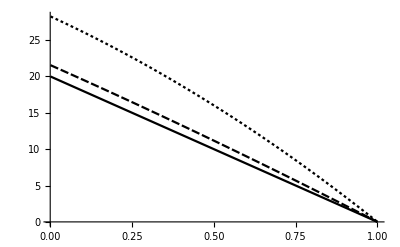

```mathematica
Plot[{P[x]-P[1],P[x]-P[1]+(C2(1+6a))/(2a+1)^2(1-x^2),P[x]-P[1]+(C1(1+6a))/(α(2a+1)^2)(1-x^2)+CalcFp[x]-CalcFp[1]},{x,0.001,1},PlotTheme->"Monochrome",PlotLegends->{T["p^\\text{кв}"],T["p\\vert_{\\beta=2}"],T["p\\vert_{\\beta=1}"]},AxesLabel->{T["\\xi"],T["\\nicefrac{p}{\\tau_s}",1.5]}]//Quiet
```

```mathematica
Export["F:\\study_dissertation\\Russian-Phd-LaTeX-Dissertation-Template\\images\\ch2\\pressure_sub1.pdf",%]
```

F:\study_dissertation\Russian-Phd-LaTeX-Dissertation-Template\images\ch2\pressure_sub1.pdf